```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
Off[RowReduce::luc]
Off[Solve::svars]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/DG_MPI/1v_Moments

## Some Testing with Hermite Functions (normalized)

```mathematica
f0[c_]=1/(√(2π))Exp[-c^2/2];
fM[c_]=(c v-θ/2+(c^2 θ)/2+ρ)f0[c];
H[i_,c_]=1/(√Gamma[i+1] 2^(i/2))HermiteH[i,c/√2];

fG[c_,n_]:=∑_(k=0)^(n-1) α[k]H[k,c]f0[c];
fL2[c_,n_]:=∑_(k=0)^(n-1) α[k]H2[k,c]f0[c];

(*The following routine integrates the following expressions ∫_0^∞ H[n,c]H[m,c]f0[c]ⅆc *)
```

```mathematica
HSpcInt[n_,m_]:=Which[m==n,1/2,OddQ[m-n],1/(√(2 π))(√(n!m!))/(n!)(∑_(i=1)^n (2^(1/2 (1-2 i+m+n)) π)/(Gamma[(i-m)/2] Gamma[2-i+m] Gamma[1/2 (1+i-n)])+((m-n-2)!!(-1)^((m-n-1)/2))/((m-n)!)),EvenQ[m-n],0];
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]
```

## Equations for α_j, incl. Eigenvalues

(0 | 1 | 0 | 0
1 | 0 | √2 | 0
0 | √2 | 0 | √3
0 | 0 | √3 | 0)

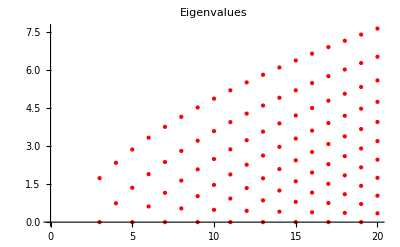

```mathematica
AA[n_]:=Table[If[i==j+1,√i,If[i==j-1,√(i+1),0]],{i,0,n-1},{j,0,n-1}]

MatrixForm[AA[4]]
ListPlot[N[Table[Thread[{Table[n,{i,1,If[OddQ[n],(n)/2+1,(n)/2]}],N[Select[Eigenvalues[AA[n]],#≥0&]]}],{n,3,20}]],PlotLabel->"Eigenvalues",PlotStyle->{{Red,Thick,PointSize[Large]}}]
```

```mathematica
returnP[nvar_]:=Module[{P},
P=-IdentityMatrix[nvar];
P⟦1,1⟧=0;
P⟦2,2⟧=0;
P⟦3,3⟧=0;
P
]
```

## Boundary Matrices

```mathematica
Clear[MatBoe]
```

### Mat Aoe

```mathematica
(*construct Aoe*)
MatAoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=ConstantArray[0,{Length[IDOdd],Length[IDEven]}];
Do[Do[If[ii==jj,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧],If[jj==ii+1,result⟦ii,jj⟧=Sqrt[IDOdd⟦ii⟧+1]]],{jj,1,Length[IDEven]}],{ii,1,Length[IDOdd]}];

result

]
```

### Mat Boe

```mathematica
(*With the assumption that the normal points from the gas into the wall.*)
MatBoe[n_]:=Module[{result,numOdd,numEven,IDOdd,IDEven,rhoW},
IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];

result=Flatten[ConstantArray[0,{Length[IDOdd],1}]];


(*First we compute the density at the wall*)
rhoW=Expand[ρW/.Solve[(Expand[(ρW HSpcInt[1,0]+0 HSpcInt[1,1]+θW/√2 HSpcInt[1,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[1,2j]])==0,ρW]⟦1⟧];


(*2 comes from the left hand side of the boundary conditions and the minus comes from the direction of the normal*)
Do[result⟦ii⟧=-2((rhoW HSpcInt[IDOdd⟦ii⟧,0]+θW/√2 HSpcInt[IDOdd⟦ii⟧,2])-∑_(j=0)^((n-1)/2) α[2j]HSpcInt[IDOdd⟦ii⟧,2j]),{ii,1,Length[IDOdd]}];

CoefficientArrays[result,Map[α[#]&,IDEven]]⟦2⟧
]
```

### Mat Onsager

```mathematica
MatOnsager[n_]:=Module[{Btilde,result},

Btilde=MatBoe[n]⟦1;;-1,1;;Length[MatBoe[n]]⟧;
Btilde.Inverse[MatAoe[n]⟦1;;-1,1;;Length[MatAoe[n]]⟧]
]
```

## Construct Boundary Conditions

### core routine

```mathematica
(*flag == 0 for MBCs,flag == 1 for OBCs*)
ConstructStableBC[n_]:=Module[{IDEven,IDOdd,result,Boe},

IDOdd = If[EvenQ[n],Range[1,n-1,2],Range[1,n-2,2]];
IDEven = If[EvenQ[n],Range[0,n-2,2],Range[0,n-1,2]];
result=Flatten[ConstantArray[0,{Length[IDOdd]-1}]];

Boe=MatOnsager[n].MatAoe[n];

(*we neglect the first boundary condition*)
Do[result⟦ii⟧=α[IDOdd⟦ii+1⟧]-Boe⟦ii+1,All⟧.Map[α[#]&,IDEven]+Boe⟦ii+1,2⟧/(√2)θW,{ii,1,Length[IDOdd]-1}];

Expand[Simplify[result]]
]
```

### Boundary Conditions

```mathematica
(*we are ignoring the very first equation.*)
Do[bcMBC[ii]=ConstructStableBC[ii],{ii,50,50}];
```

```mathematica
bcMBC[6]
```

{(2 θW)/(√(3 π))-2 √(2/(3 π)) α[2]+α[3]-2/3 √(2/π) α[4],-(2 θW)/(√(15 π))+2 √(2/(15 π)) α[2]-2 √(2/(5 π)) α[4]+α[5]}

## Solving Routines

### solve primal (heat conduction)

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolution[nvar_,kn_,thetaw_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];

coef[0,4]=Kn k[0]; (*heat flux constant*)

(*the following ansatz is the particular solution to the problem. The problem is linear therefore it is enough to consider upto first order polynomials as the ansatz. Such ansatz is only possible because of a bounded domain. On an unbounded domain, we cannot do this.*)

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+alpha B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

(*The following additon of the eigenmodes is the homogeneous solution to the problem. But why the term C0B0?*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->thetaw})==0],Table[k[i],{i,0,nvar/2-2}]]⟦1⟧;

Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}
]
```

### solve primal (poisson heat conduction)

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolutionPoisson[nvar_,kn_,thetaw_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc},
A0=AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦3⟧=-1;

(*the following ansatz is the particular solution to the problem. The problem is linear therefore it is enough to consider upto first order polynomials as the ansatz. Such ansatz is only possible because of a bounded domain. On an unbounded domain, we cannot do this.*)

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

SymmetryConditions=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];SymmetryConditions⟦(ii+1)/2⟧=(k[ii]->(Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧])k[ii+1]),{ii,1,Length[λ],2}];

(*The following additon of the eigenmodes is the homogeneous solution to the problem. But why the term C0B0?*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];


bc=bcinput;
bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->1/2};
solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->0})==0],Join[{C0},Table[k[i],{i,0,nvar/2-2}]]]⟦1⟧;

Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}
]
```

```mathematica
Clear[trial]
trial = GetSolution[20,0.1,1,bcMBC[20]]⟦3⟧;
```

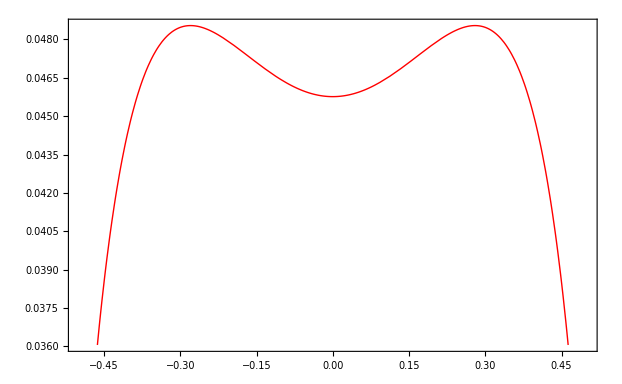

```mathematica
Plot[trial,{x,-0.5,0.5}]
```

### solve adjoint

```mathematica
Clear[nvar,kn,thetaw,A0,P0,λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC]

(*flag = 0 for unstable, flag == 1 for stable*)
GetSolutionAdjoint[nvar_,kn_,bcinput_]:=Block[{λ0,λ,λPlus,v,vv,B0,alpha,coef,Kn,vW,k,Ansatz,Coefs,SymmetryConditions,solution,res,bcEqn,solBC,bc,Signum},

A0=-AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{λ0,vv}=Eigensystem[{P0,1.0A0}];
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,λ}],1]];

λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];
(*λ=Flatten[Table[{-Rationalize[λ⟦ii⟧,0],Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];*)
λPlus=Select[λ,(#>0)&];

B0=Table[0,{i,1,nvar}];
B0⟦3⟧=1;

(*the following ansatz is the particular solution to the problem. The problem is linear therefore it is enough to consider upto first order polynomials as the ansatz. Such ansatz is only possible because of a bounded domain. On an unbounded domain, we cannot do this.*)

Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,5}],{ii,1,nvar}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,5}],{ii,1,nvar}]],coef[_,_]];

Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]-B0 x,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};


Signum=Table[0,{ii,1,Length[λ],2}];
Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];
SymmetryConditions=Table[k[ii]->Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}];

(*The following additon of the eigenmodes is the homogeneous solution to the problem.*)
solution=ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]];

res=Thread[Table[α[i],{i,0,nvar-1}]->solution/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]];

bc=bcinput;

bcEqn=Table[bc⟦i⟧,{i,1,nvar/2-1}]/.res/.{x->-1/2};

solBC=Solve[Thread[(bcEqn/.{Kn->kn,θW->0})==0],Flatten[{C0,Table[k[i],{i,1,nvar/2-2}]}]]⟦1⟧;

Table[α[i],{i,0,nvar-1}]/.res/.solBC/.{Kn->kn}

]

ManufacturedAdjoint[nvar_]:=Module[{Ax,P0,F,U},

U=Flatten[ConstantArray[0,{nvar,1}]];

U⟦2⟧=Cos[π x];

A0=-AA[nvar];
P0=SparseArray[{{i_,i_}->-1},nvar];
P0⟦1,1⟧=0;
P0⟦2,2⟧=0;
P0⟦3,3⟧=0;

{U,A0.D[U,x]}

]
```

### compute error

```mathematica
ErrorAdjoint[primal_,adjoint_,dx_]:=Module[{error,grid,Ax,P,Kn},

Ax = AA[Length[adjoint]]⟦All,1;;Length[primal]⟧;

P=SparseArray[{{i_,i_}->-1},Length[adjoint]];
P⟦1,1⟧=0;
P⟦2,2⟧=0;
P⟦3,3⟧=0;

Kn = 0.1;
P=P⟦All,1;;Length[primal]⟧/Kn;
error = Simplify[-adjoint.Ax.D[primal,x]+adjoint.P.primal];
grid =Range[-0.5,0.5,dx];

Table[NIntegrate[error,{x,grid⟦ii⟧,grid⟦ii+1⟧}],{ii,1,Length[grid]-1}]
]

ErrorResidual[primal_,neqn_,dx_]:=Module[{error,grid,Ax,P,Kn},

Ax = AA[neqn]⟦All,1;;Length[primal]⟧;

P=SparseArray[{{i_,i_}->-1},neqn];
P⟦1,1⟧=0;
P⟦2,2⟧=0;
P⟦3,3⟧=0;
Kn = 0.1;

P=P⟦All,1;;Length[primal]⟧/Kn;
error = Simplify[Ax.D[primal,x]-P.primal];
error = error.error;
grid =Range[-0.5,0.5,dx];

Table[NIntegrate[error,{x,grid⟦ii⟧,grid⟦ii+1⟧}],{ii,1,Length[grid]-1}]
]

ErrorExact[primal_,reference_,jOmega_,dx_]:=Module[{error,grid},

error = -Simplify[(primal⟦1;;3⟧-reference⟦1;;3⟧).jOmega⟦1;;3⟧];
grid =Range[-0.5,0.5,dx];
Table[NIntegrate[error,{x,grid⟦ii⟧,grid⟦ii+1⟧}],{ii,1,Length[grid]-1}]
]
```